```mathematica
files=FileNames["*.csv",NotebookDirectory[]]
```

{/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/4.2/data.csv}

```mathematica
importfile = files⟦1⟧
```

/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/4.2/data.csv

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

```mathematica
dataset=makeDataset[raw]
```

```mathematica
dataset1=dataset[2;;-3,<|"aexp"->((√(#Nwithf))/(#pexp)&),"Texphi"->(#Texp&)|>]
```

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1
MantVal[a_]:=Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10
hiTeXForm[x_]:=Which[Head[x]===Real,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset3=dataset1[All,<|"aexp"->(hiTeXForm[#a]&),"bexp"->(hiTeXForm[#b]&)|>]
```

```mathematica
dataset4=dataset1[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"datahi.csv",dataset1,"TextDelimiters"->""]
```

/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/4.2/datahi.csv

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

FittedModel[0.004554-7.18923×10^-6 x]

0.004550.00012

-7.190.3410^-6

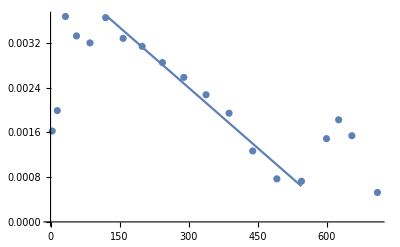

```mathematica
data=Table[{dataset1[n,"Texphi"],dataset1[n,"aexp"]},{n,19}];
fit=LinearModelFit[data[[6;;15]],{1,x},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[data],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦6;;15,1⟧],Max[data⟦6;;15,1⟧]}]]
```

```mathematica
Solve[4.553996347352668-0.007189231958478416 x==0,x]
```

{{x→633.447}}

```mathematica
(0.004550.00012)/(-7.190.3410^-6)
```

-633.34.